```mathematica
pi[M_,a_,b_,d_,f_,x_,θ_]:=-a*(θ-π/2)^2-b/x  - M/((d^2+f^2+x^2 +2d(f^2+x^2 Cos[θ]^2)^(1/2))^(1/2))
```

```mathematica
D[pi[M,a,b,d,f,x,θ],x]
```

```mathematica
D[pi[M,a,b,d,f,x,θ],θ]
```

```mathematica
dpidx[M,a,b,d,f,x,θ]:=b/x[ϕ]^2+(M (2 x[ϕ]+(2 d x[ϕ] Cos[θ[ϕ]]^2)/(√(f^2+x[ϕ]^2 Cos[θ[ϕ]]^2))))/(2 (d^2+f^2+x[ϕ]^2+2 d √(f^2+x[ϕ]^2 Cos[θ[ϕ]]^2))^(3/2))
```

```mathematica
dpidθ[M,a,b,d,f,x,θ]:=-2 a (-π/2+θ[ϕ])-(d M x[ϕ]^2 Cos[θ[ϕ]] Sin[θ[ϕ]])/(√(f^2+x[ϕ]^2 Cos[θ[ϕ]]^2) (d^2+f^2+x[ϕ]^2+2 d √(f^2+x[ϕ]^2 Cos[θ[ϕ]]^2))^(3/2))
```

```mathematica
L=1;
M=11590;
a=0.2957;
b=1378;
d=4943;
f=1096;
μ=15.6378
```

15.6378

{{x→InterpolatingFunction[…],θ→InterpolatingFunction[…],vx→InterpolatingFunction[…],vθ→InterpolatingFunction[…]}}

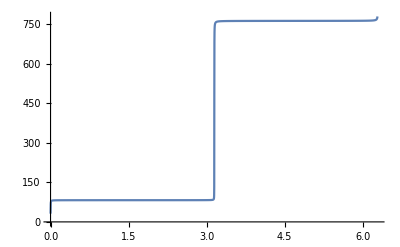

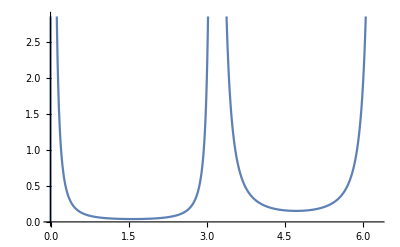

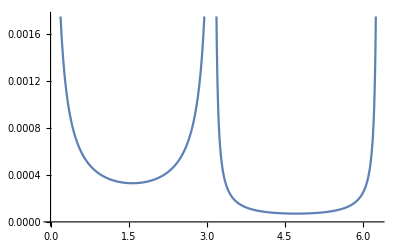

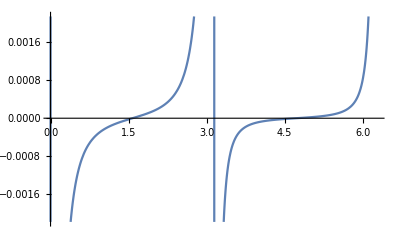

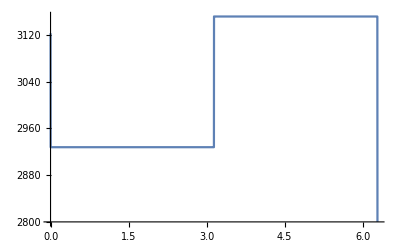

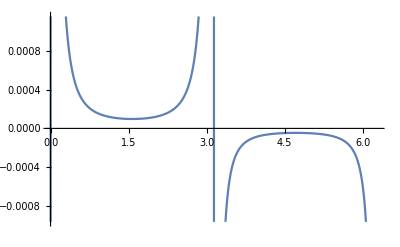

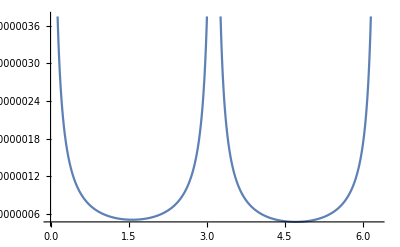

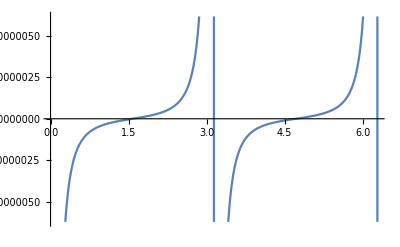

```mathematica
s=NDSolve[{vx[ϕ]==x'[ϕ] ,vθ[ϕ]==θ'[ϕ],vθ'[ϕ]== 2 vθ[ϕ]^2 Cot[θ[ϕ]]+ Sin[θ[ϕ]] Cos[θ[ϕ]]-(x[ϕ]^4 Sin[θ[ϕ]]^4)/L^2 (b/x[ϕ]^2+(M (2 x[ϕ]+(2 d x[ϕ] Cos[θ[ϕ]]^2)/(√(f^2+x[ϕ]^2 Cos[θ[ϕ]]^2))))/(2 (d^2+f^2+x[ϕ]^2+2 d √(f^2+x[ϕ]^2 Cos[θ[ϕ]]^2))^(3/2))), vx'[ϕ]==x[ϕ] vθ[ϕ]^2 +x[ϕ] Sin[θ[ϕ]]^2+(2 vx[ϕ]^2)/x[ϕ]+2 vθ[ϕ] vx[ϕ] Cot[θ[ϕ]]- (x[ϕ]^4 Sin[θ[ϕ]]^4)/L^2(-2 a (-π/2+θ[ϕ])-(d M x[ϕ]^2 Cos[θ[ϕ]] Sin[θ[ϕ]])/(√(f^2+x[ϕ]^2 Cos[θ[ϕ]]^2) (d^2+f^2+x[ϕ]^2+2 d √(f^2+x[ϕ]^2 Cos[θ[ϕ]]^2))^(3/2))), vx[0]== 0,x[0]==2 μ, vθ[0]== 1, θ[0]==π/2},{x,θ,vx,vθ},{ϕ,0,2π}]
Plot[x[ϕ]/.s,{ϕ,0,2π}]
Plot[vx[ϕ]/.s,{ϕ,0,2π}]
Plot[θ[ϕ]/.s,{ϕ,0,2π}]
Plot[vθ[ϕ]/.s,{ϕ,0,2π}]
```

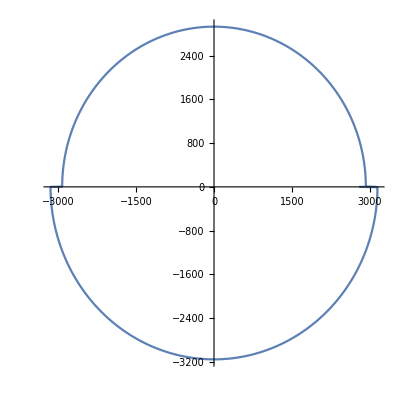

```mathematica
ParametricPlot[{x[ϕ] Cos[ϕ],x[ϕ]Sin[ϕ]}/.s,{ϕ,0,2π},AspectRatio->1]
```

```mathematica
Table[{x[ϕ] Sin[θ[ϕ]]Cos[ϕ],x[ϕ] Sin[θ[ϕ]]Sin[ϕ],x[ϕ] Cos[θ[ϕ]]}/.s,{ϕ,0,2π,0.05}];
```

```mathematica
ListPointPlot3D[Table[{x[ϕ] Sin[θ[ϕ]]Cos[ϕ],x[ϕ] Sin[θ[ϕ]]Sin[ϕ],x[ϕ] Cos[θ[ϕ]]}/.s,{ϕ,0,2π,0.05}]]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{x[ϕ] Sin[θ[ϕ]]Cos[ϕ],x[ϕ] Sin[θ[ϕ]]Sin[ϕ],x[ϕ] Cos[θ[ϕ]]}/.s,{ϕ,0,2π},PlotRange->{{-3000,3000},{-4000,4000},{2000,3000}},AspectRatio->1,AxesLabel->{x,y,z}]
```

-Graphics3D-